## From Equation (7) to Equation (11) from Heinrich et al. 2002

Ok, so start with Equation (7) and solve that differential equation for X_1.

NOTE: LOWERCASE L WILL BE USED IN PLACE OF λ CAUSE IT’S ANNOYING TO TYPE A BUNCH

```mathematica
DSolve[{x1'[t] == a1 Exp[-l t]- b1 x1[t], x1[0] == 0}, x1[t],t]
```

{{x1[t]→(a1 ⅇ^(-b1 t) (-1+ⅇ^((b1-l) t)))/(b1-l)}}

Use the above to solve for X_2:

```mathematica
FullSimplify[DSolve[{x2'[t] == a2 (a1 ⅇ^(-b1 t) (-1+ⅇ^((b1-l) t)))/(b1-l) - b2 x2[t], x2[0] == 0}, x2[t], t]]
```

{{x2[t]→(a1 a2 ⅇ^(-b2 t) (-b2 ⅇ^((b2-l) t)+b1 (-1+ⅇ^((b2-l) t))+ⅇ^((-b1+b2) t) (b2-l)+l))/((b1-b2) (b1-l) (b2-l))}}

Now we want to compute the quantities I_2, T_2, Q_2 described in Equations (4) and (5) in that order below.

```mathematica
Integrate[(a1 a2 ⅇ^(-b2 t) (-b2 ⅇ^((b2-l) t)+b1 (-1+ⅇ^((b2-l) t))+ⅇ^((-b1+b2) t) (b2-l)+l))/((b1-b2) (b1-l) (b2-l)), {t,0,∞}]
```

ConditionalExpression[(a1 a2)/(b1 b2 l),Re[b1]>0&&Re[b2]>0&&Re[l]>0]

```mathematica
Integrate[t(a1 a2 ⅇ^(-b2 t) (-b2 ⅇ^((b2-l) t)+b1 (-1+ⅇ^((b2-l) t))+ⅇ^((-b1+b2) t) (b2-l)+l))/((b1-b2) (b1-l) (b2-l)), {t,0,∞}]
```

ConditionalExpression[(a1 a2 (b1 (-1/b2^2+1/l^2)+(b2-l)/b1^2-b2/l^2+l/b2^2))/((b1-b2) (b1-l) (b2-l)),Re[b1]>0&&Re[b2]>0&&Re[l]>0]

```mathematica
Integrate[t^2(a1 a2 ⅇ^(-b2 t) (-b2 ⅇ^((b2-l) t)+b1 (-1+ⅇ^((b2-l) t))+ⅇ^((-b1+b2) t) (b2-l)+l))/((b1-b2) (b1-l) (b2-l)), {t,0,∞}]
```

ConditionalExpression[(2 a1 a2 (b1 (-1/b2^3+1/l^3)+(b2-l)/b1^3-b2/l^3+l/b2^3))/((b1-b2) (b1-l) (b2-l)),Re[b1]>0&&Re[b2]>0&&Re[l]>0]

Next we calculate S_2.  Notice the forms of I_2 and θ_2.  There the form of the numerator and denominator of Equation (10).  So getting from 7 to ten is pretty straight forward.

S_2 = I_2/(2 θ_2)= (S_o Π a_k/ b_k)/(√1 + λ^2 Σ Β_k^-2)
I_2 = (a_1 a_2)/(b_1 b_2) 1/λ= Π a_k/b_k
θ_2 = √ 1/λ^2 + 1/b_1^2+ 1/b_2^2 = √ 1 + λ^2 Σ b_k^-2

```mathematica
i = (a1 a2)/(b1 b2 l);
t1 = (a1 a2 (b1 (-1/b2^2+1/l^2)+(b2-l)/b1^2-b2/l^2+l/b2^2))/((b1-b2) (b1-l) (b2-l));
q = (2 a1 a2 (b1 (-1/b2^3+1/l^3)+(b2-l)/b1^3-b2/l^3+l/b2^3))/((b1-b2) (b1-l) (b2-l));
s2 = FullSimplify[i/(2 Sqrt[q/i- (t1/i)^2])]
theta2 = FullSimplify[Sqrt[q/i- (t1/i)^2]]
```

(a1 a2)/(2 b1 b2 √(1/b1^2+1/b2^2+1/l^2) l)

√(1/b1^2+1/b2^2+1/l^2)

Now let’s do the same the for X_3.

```mathematica
FullSimplify[DSolve[{x3'[t] == a3 (a1 a2 ⅇ^(-b2 t) (-b2 ⅇ^((b2-l) t)+b1 (-1+ⅇ^((b2-l) t))+ⅇ^((-b1+b2) t) (b2-l)+l))/((b1-b2) (b1-l) (b2-l)) - b3 x3[t], x3[0] == 0}, x3[t], t]]
```

{{x3[t]→(a1 a2 a3 ⅇ^(-b3 t) (b3 (ⅇ^((-b1+b3) t)-ⅇ^((-b2+b3) t)) l (-b3+l)+b1^2 (-b3 ⅇ^((b3-l) t)+b2 (-1+ⅇ^((b3-l) t))+ⅇ^((-b2+b3) t) (b3-l)+l)+b2^2 (b3 ⅇ^((b3-l) t)-l+ⅇ^((-b1+b3) t) (-b3+l))+b2 (-b3^2 ⅇ^((b3-l) t)+l^2+ⅇ^((-b1+b3) t) (b3-l) (b3+l))+b1 (b3^2 ⅇ^((b3-l) t)-b2^2 (-1+ⅇ^((b3-l) t))-l^2+ⅇ^((-b2+b3) t) (-b3^2+l^2))))/((b1-b2) (b1-b3) (b2-b3) (b1-l) (b2-l) (b3-l))}}

```mathematica
Integrate[(a1 a2 a3 ⅇ^(-b3 t) (b3 (ⅇ^((-b1+b3) t)-ⅇ^((-b2+b3) t)) l (-b3+l)+b1^2 (-b3 ⅇ^((b3-l) t)+b2 (-1+ⅇ^((b3-l) t))+ⅇ^((-b2+b3) t) (b3-l)+l)+b2^2 (b3 ⅇ^((b3-l) t)-l+ⅇ^((-b1+b3) t) (-b3+l))+b2 (-b3^2 ⅇ^((b3-l) t)+l^2+ⅇ^((-b1+b3) t) (b3-l) (b3+l))+b1 (b3^2 ⅇ^((b3-l) t)-b2^2 (-1+ⅇ^((b3-l) t))-l^2+ⅇ^((-b2+b3) t) (-b3^2+l^2))))/((b1-b2) (b1-b3) (b2-b3) (b1-l) (b2-l) (b3-l)), {t,0,∞}]
```

ConditionalExpression[(a1 a2 a3)/(b1 b2 b3 l),Re[b1]>0&&Re[b2]>0&&Re[b3]>0&&Re[l]>0]

```mathematica
Integrate[t(a1 a2 a3 ⅇ^(-b3 t) (b3 (ⅇ^((-b1+b3) t)-ⅇ^((-b2+b3) t)) l (-b3+l)+b1^2 (-b3 ⅇ^((b3-l) t)+b2 (-1+ⅇ^((b3-l) t))+ⅇ^((-b2+b3) t) (b3-l)+l)+b2^2 (b3 ⅇ^((b3-l) t)-l+ⅇ^((-b1+b3) t) (-b3+l))+b2 (-b3^2 ⅇ^((b3-l) t)+l^2+ⅇ^((-b1+b3) t) (b3-l) (b3+l))+b1 (b3^2 ⅇ^((b3-l) t)-b2^2 (-1+ⅇ^((b3-l) t))-l^2+ⅇ^((-b2+b3) t) (-b3^2+l^2))))/((b1-b2) (b1-b3) (b2-b3) (b1-l) (b2-l) (b3-l)), {t,0,∞}]
```

ConditionalExpression[(a1 a2 a3 (b1 b2 b3+b2 b3 l+b1 (b2+b3) l))/(b1^2 b2^2 b3^2 l^2),Re[b1]>0&&Re[b2]>0&&Re[b3]>0&&Re[l]>0]

```mathematica
Integrate[t^2(a1 a2 a3 ⅇ^(-b3 t) (b3 (ⅇ^((-b1+b3) t)-ⅇ^((-b2+b3) t)) l (-b3+l)+b1^2 (-b3 ⅇ^((b3-l) t)+b2 (-1+ⅇ^((b3-l) t))+ⅇ^((-b2+b3) t) (b3-l)+l)+b2^2 (b3 ⅇ^((b3-l) t)-l+ⅇ^((-b1+b3) t) (-b3+l))+b2 (-b3^2 ⅇ^((b3-l) t)+l^2+ⅇ^((-b1+b3) t) (b3-l) (b3+l))+b1 (b3^2 ⅇ^((b3-l) t)-b2^2 (-1+ⅇ^((b3-l) t))-l^2+ⅇ^((-b2+b3) t) (-b3^2+l^2))))/((b1-b2) (b1-b3) (b2-b3) (b1-l) (b2-l) (b3-l)), {t,0,∞}]
```

ConditionalExpression[1/(b1^3 b2^3 b3^3 l^3)2 a1 a2 a3 (b2^2 b3^2 l^2+b1 b2 b3 l (b3 l+b2 (b3+l))+b1^2 (b3^2 l^2+b2 b3 l (b3+l)+b2^2 (b3^2+b3 l+l^2))),Re[b1]>0&&Re[b2]>0&&Re[b3]>0&&Re[l]>0]

Notice I_3, Q_3, θ_3 are following the pattern.

```mathematica
i = (a1 a2 a3)/(b1 b2 b3 l);
t1 = (a1 a2 a3 (b1 b2 b3+b2 b3 l+b1 (b2+b3) l))/(b1^2 b2^2 b3^2 l^2);
q = 1/(b1^3 b2^3 b3^3 l^3)2 a1 a2 a3 (b2^2 b3^2 l^2+b1 b2 b3 l (b3 l+b2 (b3+l))+b1^2 (b3^2 l^2+b2 b3 l (b3+l)+b2^2 (b3^2+b3 l+l^2)));
s3 = FullSimplify[i/(2 Sqrt[q/i- (t1/i)^2])]
```

```mathematica
(a1 a2 a3)/(2 b1 b2 b3 √(1/b1^2+1/b2^2+1/b3^2+1/l^2) l)
```

Ok now mathematica won’t cooperate as much so here’s what we have to do.  To analyze the change in signal amplitude, we are going to subtract S_2 from S_3.

S_3 - S_2 = (a_1 a_2 a_3)/(2 λ b_1 b_2 b_3 θ_3)- (a_1 a_2)/(2 λ b_1 b_2 θ_2)= (a_1 a_2)/(2 λ b_1 b_2) ( a_3/(b_3 θ_3)- 1/θ_2)

We want amplification, which means we require that S_3 - S_2 > 0.  So,

(a_1 a_2)/(2 λ b_1 b_2) ( a_3/(b_3 θ_3)- 1/θ_2) > 0  

This is equivalent to saying 

 ( a_3/(b_3 θ_3)- 1/θ_2) > 0  
 
 because the constants outside the parentheses are all possible so they cannot affect the sign of the outcome.  The main problem here is isolating b_3 because θ_3 also depends on b_3.  However, we can see that
 
 b_3 θ_3 < a_3 θ_2
 
 That still isn’t very helpful.  So we will find a value for b_3 where S_3 = S_2 which will be an upper bound on b_3 such that there can be amplification in signal.  So,
 
 b_3 - (a_3 θ_2)/θ_3= 0
 
 Using mathematica’s solve command, we find the following:

```mathematica
Solve[b3^2- (a3^2 (1 + λ^2 (b1^-2 + b2^-2)))/(1 + λ^2(b1^-2 + b2^-2 + b3^-2)) == 0, b3]
```

{{b3→0},{b3→0},{b3→-(√(a3^2 b1^2 b2^2+a3^2 b1^2 λ^2+a3^2 b2^2 λ^2-b1^2 b2^2 λ^2))/(√(b1^2 b2^2+b1^2 λ^2+b2^2 λ^2))},{b3→(√(a3^2 b1^2 b2^2+a3^2 b1^2 λ^2+a3^2 b2^2 λ^2-b1^2 b2^2 λ^2))/(√(b1^2 b2^2+b1^2 λ^2+b2^2 λ^2))}}

We don't want b_3 to be zero and it must be positive.  So that narrows our choices to the last value provided.  Obviously mathematica hates us because it doesn’t know what form we need.

```mathematica
FullSimplify[(√(a3^2 b1^2 b2^2+a3^2 b1^2 λ^2+a3^2 b2^2 λ^2-b1^2 b2^2 λ^2))/(√(b1^2 b2^2+b1^2 λ^2+b2^2 λ^2))]
```

(√(-b1^2 b2^2 λ^2+a3^2 (b2^2 λ^2+b1^2 (b2^2+λ^2))))/(√(b2^2 λ^2+b1^2 (b2^2+λ^2)))

So now we move forward without mathematica’s aid.

b_3 = ((a_3^2( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2)) - b_1^2 b_2^2 λ^2)/( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2)))^(1/2)

First thing to do is factor out the a_3^2 and then we can separate the two numerator terms.  After factoring out, the first term becomes 1:

b_3 = a_3 (( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2))/( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2))- ((b_1^2 b_2^2 λ^2)/(a_3^2 ( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2)))))^(1/2)

b_3 = a_3 ( 1 - ((b_1^2 b_2^2 λ^2)/(a_3^2 ( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2)))))^(1/2)

Now we need to focus on that second term because we need the following

(b_1^2 b_2^2 λ^2)/( b_2^2 λ^2 + b_1^2( b_2^2 + λ^2))= θ_2^-2

To do so, first expand the bottom and then multiply by (b_1^-2 b_2^-2)/(b_1^-2 b_2^-2):
(b_1^-2 b_2^-2)/(b_1^-2 b_2^-2)(b_1^2 b_2^2 λ^2)/(b_2^2 λ^2 + b_1^2 b_2^2 + b_1^2 λ^2)= λ^2/(1 + b_1^-2 λ^2 + b_2^-2 λ^2)
Then multiply by λ^-2/λ^-2:
-> 1/(λ^-2 + b_1^-2 + b_2^-2) = 1/θ_2^2 According to Equation (9)

SO, FINALLY, we have 

b_3 = a_3 (1 - 1/(a_3^2 θ_2^2) )^(1/2) where no amplification or dampening occurs or 
b_3 < a_3 (1 - 1/(a_3^2 θ_2^2) )^(1/2) where amplification occurs!

```mathematica
sratio = 1;
al = 1;
be = .6;
nlist = {};
valuelist = {};
For[n = 1, n < 16, n++, 
val = 1/sratio Product[al/be, {i,1,n}];
nlist = Append[nlist, n];
valuelist = Append[valuelist, val]
]
nlist
valuelist
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{1.66667,2.77778,4.62963,7.71605,12.8601,21.4335,35.7225,59.5374,99.229,165.382,275.636,459.394,765.656,1276.09,2126.82}

```mathematica
alpha = 1;
beta = .3;
c = 1;
lambda = 0;
X = {};
X = AppendTo[X, (c R)/(c beta/alpha + R)];
For[i = 2, i< 5, i++,
	X = AppendTo [X,(c X[[i-1]])/(c beta/alpha+ X[[i-1]])] (* Automate the rest *)
	]
```

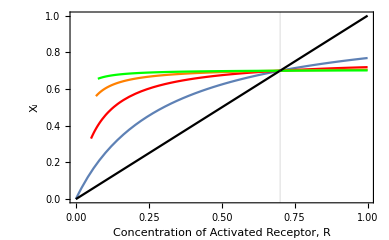

```mathematica
Show[Plot[X[[1]], {R,0,1}, PlotRange->All, GridLines->{{1-beta/alpha},{}}, Frame -> True, FrameLabel-> {"Concentration of Activated Receptor, R", "X_i"},PlotLegends->Placed[{"i=1"},{Right, Bottom}]],Plot[X[[2]], {R,0,1}, PlotStyle -> Red,PlotLegends->Placed[{"i=2"},{Right, Bottom}]],Plot[X[[3]], {R,0,1}, PlotStyle -> Orange,PlotLegends->Placed[{"i=3"},{Right, Bottom}]],Plot[X[[4]], {R,0,1}, PlotStyle -> Green,PlotLegends->Placed[{"i=4"},{Right, Bottom}]], Plot[x,{x,0,1},PlotStyle -> Black]]
```